```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

```mathematica
(*ConfigureMaTeX["pdfLaTeX"->"/Library/TeX/texbin/pdflatex","Ghostscript"->"/usr/local/bin/gs"]*)
```

```mathematica
MaTeX["x^2"]
```

-Graphics-

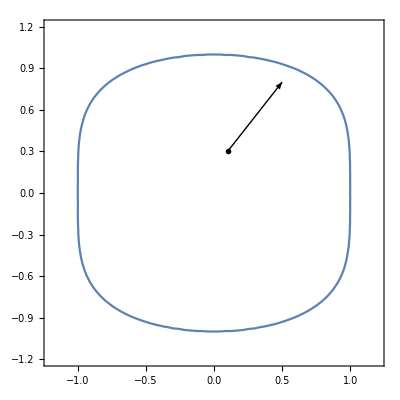

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};

ContourPlot[x^2+y^4==1,{x,-1.2,1.2},{y,-1.2,1.2},BaseStyle->texStyle,
Epilog->{Arrow[{{0.1,0.3},{0.5,0.80}}],Inset[MaTeX["x^2+y^4=1",Magnification->2],{0.1,0.3},Scaled[{0.5,1}]]}]
```

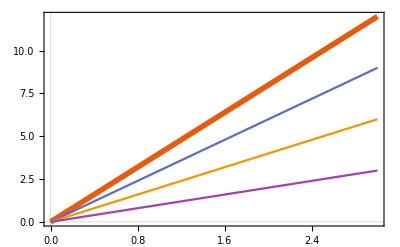

```mathematica
Plot[{4 t,3 t,2 t,t},{t,0,3},AxesOrigin->{0,0},FrameLabel->{MaTeX["t (years)"],MaTeX["C (mg/l)"]},PlotTheme->"Scientific",PerformanceGoal->"Quality",PlotRange->Full,
BaseStyle->texStyle,PlotLegends->LineLegend[{MaTeX["x^2+y^4=1",Magnification-> 1.5],MaTeX["N"],MaTeX["\int_z^w dz"],MaTeX["\sum_{k=1}^n \Gamma(n)"]},LegendFunction->Frame],PlotStyle->{Thickness[0.01],Automatic,Automatic,Automatic}]
```